# Support Vector Machine

Yang Long

#### Sigmoid Function

g(z)=1/(1+e^-z)

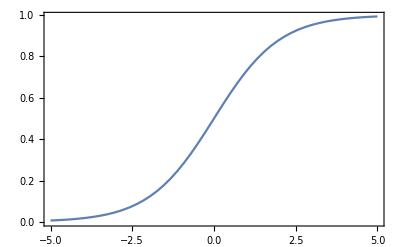

```mathematica
Plot[1/(1+Exp[-z]),{z,-5,5},Axes->False,Frame->True]
```

#### Logistic Classification

h_θ(x)=g(θ^T x)=1/(1+e^(-θ^Tx))

P(y=1|x,θ)=h_θ(x)
P(y=0|x,θ)=1-h_θ(x)

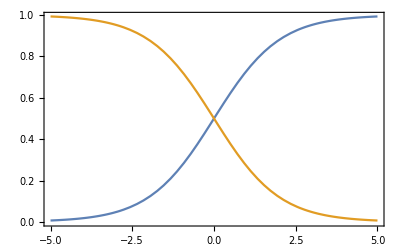

```mathematica
Plot[{1/(1+Exp[-x]),1-1/(1+Exp[-x])},{x,-5,5},Axes->False,Frame->True]
```

#### Margin

Super Plane:  y=f(x)=ω^T x+b

##### Functional Margin

γ̂=y(ω^T x+b)=y f(x)

γ̂= min (γ̂)_i (i=1,...,n)

##### Geometrical Margin

For point x, γ

x=x_0+γ ω/(||ω||)

So as to f((x⃗)_0)=0, we have

f(x)=f(x_0+γ  ω/(||ω||))=ω^T x_0+γ(ω^T ω)/(||ω||)+b=γ(ω^T ω)/(||ω||)=γ ||ω||

γ=(f(x))/(||ω||)=(ω^T x+b)/(||ω||)

The geometrical margin:

γ̃=y γ=y(ω^T x+b)/(||ω||)=(γ̂)/(||ω||)

#### Maximum Margin Classifier

max γ̃

y_i(ω^T x_i+b)=(γ̂)_i≥ γ̂, i=1,...,n

Set γ̂=1, minimize functional margin firstly, and then maximize geometrical margin.  So we have

max 1/(||ω||), s.t. y_i(ω^T x_i+b)≥ 1,i=1,...,n

Lack of full mathematical evidence and derivation

#### Form conversion

SVM eigenequation

max 1/(||ω||)   s.t., y_i(ω^T x_i+b)≥ 1, i=1,..., n

min 1/2||ω(||)^2 s.t. y_i(ω^T x_i+b)≥ 1, i=1,...,n

To minimize 1/2||ω(||)^2 with the linear restricted conditions is a classical Quadratic programming (QP).

#### Lagrange Multiplier

L(ω,b,α)=1/2||ω(||)^2-(∑_(i=1))^n α_i(y_i(ω^T x_i+b)-1)

θ(ω)=max_(α_i≥ 0) L(ω,b,α)

min_(ω,b) θ(ω)=min_(ω,b) max_(α_i≥ 0) L(ω,b,α)=p^*

max_(α_i≥ 0) min_(ω,b) L(ω,b,α)=d^*

d^*≤ p^*

so max_(α_i≥ 0) min_(ω,b) L(ω,b,α) will be the new eigenequation. (1)Minimize L by ω, b firstly; (2)Maximize L by α.

#### Karush–Kuhn–Tucker(KKT) conditions

In Mathematical optimization, the KKT conditions are first order necessary conditions for a solution in nonlinear programming to be optimal, provided that some regularity conditions are satisfied.

min f(x)
s.t.  h_j(x)=0, j=1,...,m;  g_k(x)≤0, k=1,...,l;   x ∈ X ⊂ℝ^n

Suppose that the objective function f:ℝ^n→ ℝ and the constraint functions g_i:ℝ^n→ ℝ and h_j:ℝ^n→ ℝ are continuously differentiable at a point x^*. If x^* is a local optimum and the optimization problem satisfies some regularity conditions, then there exist constants μ_i(i=1,...,m) and λ_j(j=1,...,l) called KKT multipliers

##### Stationarity

For maximizing f(x):

∇f(x^*)=(∑_(i=1))^m μ_i∇g_i(x^*)+(∑_(j=1))^l λ_j∇h_j(x^*)

For minimizing f(x):

-∇f(x^*)=(∑_(i=1))^m μ_i∇g_i(x^*)+(∑_(j=1))^l λ_j∇h_j(x^*)

##### Primal feasibility

g_i(x^*)≤ 0, i=1,...,m
h_j(x^*)=0, j=1,...,l

##### Dual feasibility

μ_i≥ 0,  i=1,...,m

##### Complementary slackness

μ_i g_i(x^*)=0,  i=1,...,m

#### Duality (optimization)

Duality play an import role in optimization and formulation of SVM, especially for kernel function.

Lack of deep comprehension

##### Minimize L by ω, b firstly

(∂L)/(∂ω)=0→ ω=(∑_(i=1))^n α_i y_i x_i
(∂L)/(∂b)=0→ (∑_(i=1))^n α_i y_i=0

Put them into L:

L(ω,b,α)=1/2||ω(||)^2-(∑_(i=1))^n α_i(y_i(ω^T x_i+b)-1)

So we have:

L(ω,b,α)=1/2(∑_(i,j=1))^n α_i α_j y_i y_j x_i^T x_j-(∑_(i,j=1))^n α_i α_j y_i y_j x_i^T x_i-b(∑_(i=1))^n α_i y_i+(∑_(i=1))^n α_i
=(∑_(i=1))^n α_i-1/2(∑_(i,j=1))^n α_i α_j y_i y_j x_i^T x_j

Here, no more ω and b in formula, because:

ω=(∑_(i=1))^n α_i y_i x_i ;   b^*=-(max_(i:y_i=-1) ω^(*T)x_i+min_(i:y_i=1) ω^(*T)x_i)/2

The optimal problem has been converted into the form:

max_α (∑_(i=1))^n α_i-1/2(∑_(i,j=1))^n α_i α_j y_i y_j x_i^T x_j
s.t. α_i≥ 0, i=1,...,n
(∑_(i=1))^n α_i y_i=0

#### Sequential Minimal Optimization(SMO)

#### Linearly Un-Separable

Hyper-plane:

f(x)=ω^T x+b

ω=(∑_(i=1))^n α_i y_i x_i

f(x)=((∑_(i=1))^n α_i y_i x_i)x+b=(∑_(i=1))^n α_i y_i⟨x_i,x⟩+b

Only the coefficients α of supporting vector are valid (not zero) and these supporting vectors contribute to the classification and regression. Thus these algorithm is called supporting vector machine. Non-supporting vectors make no or little influence on the hyper plane, which mainly decide the effect and conclusion of classification. These non-supporting vectors will not participate the calculation during classificating and we can ignore them. (Same case in the physics, only the electrons surrounding the surface of Fermi surface will contribute to the conductivity)

For supporting vector:

y_i(ω^T x_i+b)-1=0

For non-supporting vector:

y_i(ω^T x_i+b)-1≥ 0

#### Kernel

For non-linear case, the solution of SVM is to choose a kernel function to project data into higher-dimensional space to solve the linearly un-separable problem in the original space. For example, a circle in 2D space can be project into a plan in 3D plane.

Input space →  Feature space→  Output space(same as input space)

Nonlinear SVM:

f(x)=(∑_(i=1))^N ω_i ϕ_i(x)+b

f(x)=(∑_(i=1))^N α_i y_i⟨ϕ(x_i)·ϕ(x)⟩+b

Define kernel function k(x,z)=⟨ϕ(x)·ϕ(z)⟩

##### Nonlinear Data

For space {X_1,X_2}, the hyper plane:

a_1 X_1+a_2 X_1^2+a_3 X_2+a_4 X_2^2+a_5 X_1 X_2+a_6=0

For space {Z_1=X_1,Z_2=X_1^2,Z_3=X_2,Z_4=X_2^2,Z_5=X_1 X_2}, the converted hyper plane:

(∑_(i=1))^5 a_i Z_i+a_6=0

Through the projection ϕ:ℝ^2→ℝ^5, the circle in space {X_i} will transfer into the plane in space {Z_i}, the original data is linearly un-separable in space {X_i} while is linearly separable in space {Z_i}.

f(x)=(∑_(i=1))^n α_i y_i⟨x_i,x⟩+b

f(x)=(∑_(i=1))^N α_i y_i⟨ϕ(x_i)·ϕ(x)⟩+b

max_α (∑_(i=1))^n α_i-1/2(∑_(i,j=1))^n α_i α_j y_i y_j⟨ϕ(x_i)·ϕ(x_j)⟩
s.t. α_i≥ 0, i=1,...,n
(∑_(i=1))^n α_i y_i=0

Naive transformation is computationally expensive due to the explosive increasement of dimensions.

For example, x_1=(η_1
η_2), x_2=(ξ_1
ξ_2), so

⟨ϕ(x_1),ϕ(x_2)⟩=η_1 ξ_1+η_1^2 ξ_1^2+η_2 ξ_2+η_2^2 ξ_2^2+η_1 η_2 ξ_1 ξ_2

But reminding that:

(⟨x_1,x_2⟩+1)^2=2 η_1 ξ_1+η_1^2 ξ_1^2+2 η_2 ξ_2+η_2^2 ξ_2^2+η_1 η_2 ξ_1 ξ_2+1

⟨ϕ(x_1),ϕ(x_2)⟩ means the computations happen in high-dimensional space, while (⟨x_1,x_2⟩+1)^2 means that they still happen in original space. So by achieving coordinate transformation implicitly, we define the inner product function in this case as Kernel function, i.e., κ(x_1,x_2)=(⟨x_1,x_2⟩+1)^2.

f(x)=(∑_(i=1))^n α_i y_i κ(x_i,x)+b

max_α (∑_(i=1))^n α_i-1/2(∑_(i,j=1))^n α_i α_j y_i y_j κ(x_i,x_j)
s.t. α_i≥ 0, i=1,...,n
(∑_(i=1))^n α_i y_i=0

Using kernel function can avoid the expensive computation in high-dimensional space.

##### Classical Kernels

Gaussian Kernels

κ(x_1,x_2)=e^(-(||x_1-x_2(||)^2)/(2 σ^2))

#### Outliers

Although the nonlinear cases in the original space may be linearly separated in higher-dimensional space, some cases are still hard to deal with. The reasones behind these may be the noises among the data.

The existence of noises may cause the distortion of hyper plane. To avoid this situation, we can the some position bias in some degree.

y_i(ω^T x_i+b)≥ 1-ξ_i, i =1,...,n

where ξ_i≥ 0 is called as slack variable.

min 1/2||ω(||)^2+C (∑_(i=1))^n ξ_i
s.t., y_i(ω^T x_i+b)≥ 1-ξ_i, i =1,...,n
ξ_i≥ 0, i =1,...,n

The larange function with considering outliers:

L(ω,b,ξ,α,r)=1/2||ω(||)^2+C (∑_(i=1))^n ξ_i-(∑_(i=1))^n α_i(y_i(ω^T x_i+b)-1+ξ_i)-(∑_(i=1))^n r_i ξ_i

Similarily as above, we have

(∂L)/(∂ω)=0→ ω=(∑_(i=1))^n α_i y_i x_i
(∂L)/(∂b)=0→ (∑_(i=1))^n α_i y_i=0
(∂L)/(∂ξ_i)=0→ C-α_i-r_i=0, i=1,...,n

Thus,

max_α (∑_(i=1))^n α_i-1/2(∑_(i,j=1))^n α_i α_j y_i y_j⟨x_i,x_j⟩
s.t., 0≤α_i≤C, i=1,...,n
 (∑_(i=1))^n α_i y_i=0

#### Summary

##### Primal Formulation

max 1/2(∑_(i=1))^n ω_i^2+C (∑_(i=1))^N ξ_i
s.t. y_i(ω^T x_i+b)≥ 1-ξ_i, for i = 1,...,N

##### Dual Formulation

max (∑_(i=1))^n α_i-1/2(∑_(i,j=1))^N α_i α_j y_i y_j⟨x_i,x_j⟩
s.t., 0≤α_i≤ C  for i=1,...,N
 (∑_(i=1))^N α_i y_i=0

##### Kernel Formulation

max (∑_(i=1))^n α_i-1/2(∑_(i,j=1))^N α_i α_j y_i y_j κ(x_i,x_j)
s.t., 0≤α_i≤ C  for i=1,...,N
 (∑_(i=1))^N α_i y_i=0